## General bifurcation figures

```mathematica
blRs={AxesStyle->Black,LabelStyle->Directive[Black,12],GridLinesStyle->Directive[Black,Dotted]};
```

#### TD plane; behaviors

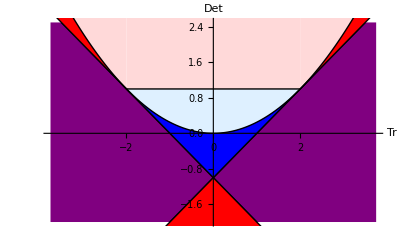

```mathematica
plotBF=Show[Plot[{tr^2/4,tr-1,-tr-1},{tr,-3.75,3.75},PlotRange->{-2,2.5},PlotStyle->{{Black,Thin}},Filling->{2->{{3},Purple}},AxesLabel->{"Tr","Det"}],Plot[{1,tr^2/4,Abs@tr-1,-Abs@tr-1,5},{tr,-2,2},PlotStyle->{{Black,Thin}},Filling->{2->{{1},LightBlue},3->{{2},Blue},4->{Bottom,Red},1->{{5},LightRed}}],Plot[{tr^2/4,Abs@tr-1},{tr,-5,-2},PlotStyle->{{Black,Thin}},Filling->{2->{{1},Red},2->{Top,LightRed}}],Plot[{tr^2/4,Abs@tr-1},{tr,2,5},PlotStyle->{{Black,Thin}},Filling->{2->{{1},Red},2->{Top,LightRed}}],blRs]
```

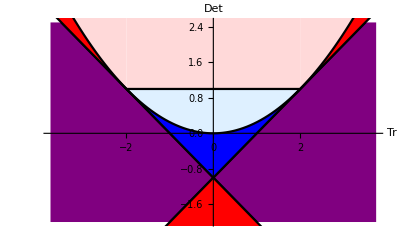

```mathematica
plotBF3=Show[Plot[{tr^2/4,tr-1,-tr-1},{tr,-3.75,3.75},PlotRange->{-2,2.5},PlotStyle->{{Black}},Filling->{2->{{3},Purple}},AxesLabel->{"Tr","Det"}],Plot[{1,tr^2/4,Abs@tr-1,-Abs@tr-1,5},{tr,-2,2},PlotStyle->{{Black}},Filling->{2->{{1},LightBlue},3->{{2},Blue},4->{Bottom,Red},1->{{5},LightRed}}],Plot[{tr^2/4,Abs@tr-1},{tr,-5,-2},PlotStyle->{{Black}},Filling->{2->{{1},Red},2->{Top,LightRed}}],Plot[{tr^2/4,Abs@tr-1},{tr,2,5},PlotStyle->{{Black}},Filling->{2->{{1},Red},2->{Top,LightRed}}],blRs]
```

```mathematica
SwatchLegend[{Red,Blue,Purple,LightRed,LightBlue},{"source","sink","saddle","spiral source","spiral sink"}]
```

```mathematica
spsink=With[{f={ Sin[x]/x^2,Cos[x]/x^2}},Show[ParametricPlot[f/.x->t,{t,8,25},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Table[{(*Hue[t/(2 Pi),1,.8],*)Arrowheads[.06],Arrow[{f,Normalize[D[f,x]]/1000+f}]}/. x->t,{t,8,25,2}]]]];
```

```mathematica
spsource=With[{f={ Sin[x]/x^2,Cos[x]/x^2}},Show[ParametricPlot[f/.x->t,{t,8,25},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Table[{(*Hue[t/(2 Pi),1,.8],*)Arrowheads[.06],Arrow[{f,Normalize[-D[f,x]]/1000+f}]}/. x->t,{t,8,25,2}]]]];
```

```mathematica
source=With[{f={{t,2t},{t,-t},{-t,-2t},{-t,t}}},Show[ParametricPlot[f,{t,.2,1},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Flatten[Table[{Arrowheads[.1],Arrow[{f,D[f,t]/10+f}⟦;;,ii⟧/.t->s]},{s,.2,1,.2},{ii,4}],1]]]];
```

```mathematica
sink=With[{f={{t,2t},{t,-t},{-t,-2t},{-t,t}}},Show[ParametricPlot[f,{t,.2,1},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Flatten[Table[{Arrowheads[.1],Arrow[{f,-D[f,t]/10+f}⟦;;,ii⟧/.t->s]},{s,.2,1,.2},{ii,4}],1]]]];
```

```mathematica
saddle=With[{f={{t,2t},{t,-t},{-t,-2t},{-t,t}}},Show[ParametricPlot[f,{t,.2,1},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Flatten[Table[{Arrowheads[.1],Arrow[{f,{1,-1,1,-1}D[f,t]/10+f}⟦;;,ii⟧/.t->s]},{s,.2,1,.2},{ii,4}],1]]]];
```

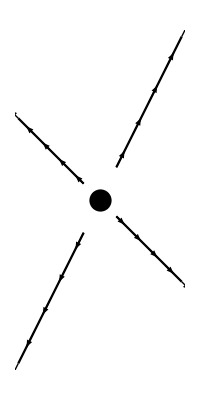
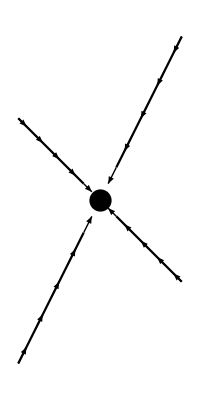
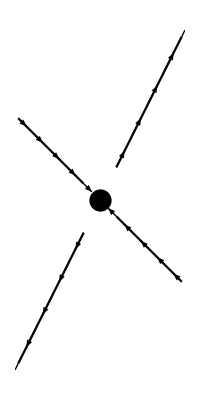
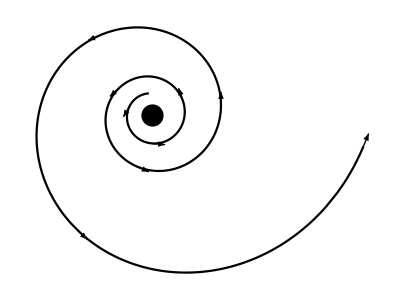
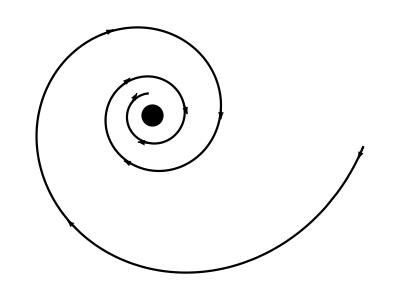

```mathematica
{source,sink,saddle,spsource,spsink}
```

```mathematica
(*stable/unstable limit cycle*){stableLC,unstableLC}=Table[With[{f={Exp[-10/x]{Sin[x],Cos[x]},Exp[10/x] {Sin[x],Cos[x]},{Sin[x],Cos[x]}}},Show[ParametricPlot[f,{x,8,40},PlotStyle->{{Black,Thin},{Black,Thin},{Black,Thick}},Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Table[{(*Hue[t/(2 Pi),1,.8],*)Arrowheads[.04],Arrow[{f⟦ii⟧,Normalize[sg D[f⟦ii⟧,x]]/1000+f⟦ii⟧}/.x->t]},{ii,3},{t,10,40,9}]]]],{sg,{1,-1}}];
```

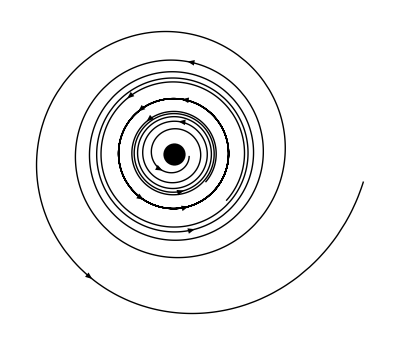
α<0 | α>0
-Graphics- | -Graphics-

```mathematica
TableForm[{{unstableLC,spsource}},TableHeadings->{None,{"α<0","α>0"}}]
```

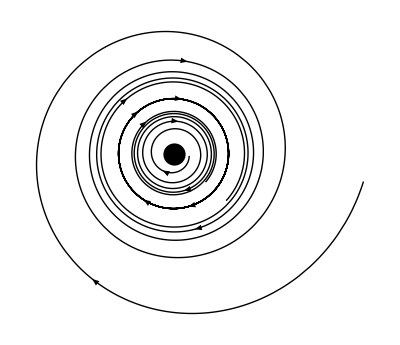
α<0 | α>0
-Graphics- | -Graphics-

```mathematica
TableForm[{{spsink,stableLC}},TableHeadings->{None,{"α<0","α>0"}}]
```

## System

```mathematica
Clear@zpf; zpf[{T_,L_},{ω_,κ_}]=(ω L)/(1+κ T^(2/3)L);
```

```mathematica
(*Clear@Tf; Tf[{T_,z_},{μ_}]=T Exp[μ-z];*)
Clear@Tf; Tf[{T_,z_},{μ_}]=T Exp[μ]/Exp[z];
Clear@Lf; Lf[{T_,L_},{λ_,ρ_}]=(1-λ) L+ρ T;
```

```mathematica
Clear@SysF;SysF[{T_,L_},{ω_,κ_,μ_,ρ_,λ_}]:={Tf[{T,zpf[{T,L},{ω,κ}]},{μ}],
Lf[{T,L},{λ,ρ}]}
```

```mathematica
var={T,L};
par={ω,κ,μ,ρ,λ};
```

```mathematica
(*equilibria*)
κeqR=κ->(-λ μ+T ρ ω)/(T^(5/3) μ ρ);
λeqR=λ->-(T ρ (T^(2/3) κ μ-ω))/μ;
ωeqR=ω->(μ (λ+T^(5/3) κ ρ))/(T ρ);
LeqR=L->(T ρ/λ);

(*saddle-node bifurcation*)
TbfR=T->(5 λ μ)/(2 ρ ω);
κbfR=κ->(3 (2/5)^(2/3) ω)/(5 μ ((λ μ)/(ρ ω))^(2/3));
λbfR=λ->(6 √(3/5) ρ ω^(5/2))/(25 κ^(3/2) μ^(5/2));
ωbfR=ω->(5  κ^(3/5) λ^(2/5) μ)/(2^(2/5)3^(3/5) ρ^(2/5));
(*NS bifurcation*)
Tb2fR=T->(λ (-2+5 λ) μ^2)/((-2 μ+λ (3+2 μ)) ρ ω);
κb2fR=κ->(3 λ^(1/3) ρ^(2/3)ω^(5/3)(1-μ)(2 μ-λ (3+2 μ))^(2/3))/((2-5 λ)^(5/3) μ^(10/3));
(*jacobian*)
J=Simplify[D[SysF[var,par],{var}]/.LeqR];
```

```mathematica
(*td-det relationshio at equilibrium*)deteqR=(5 λ^2 μ^2+T (3+2 μ) ρ ω-λ (2 μ^2+3 T ρ ω+2 T μ ρ ω))/(3 T ρ ω);(*(1-λ)(1+(2μ)/3) to -∞*)
treqR=2-λ+(2 μ)/3-(2 λ μ^2)/(3 T ρ ω);(*-∞ to 2+(2μ)/3-λ*)
deteqRtr=-(1-λ(5+μ-5/2 λ))+tr(1-(5λ)/2);(*slope is positive*)
(*inflection of κ^(**)*)κ2inflec=((-9+14 μ)+√((-9+14 μ)^2+40μ(3+2μ)))/(10(3+2μ));
```

## Bifurcation conditions

### Saddle node conditions

```mathematica
JSN=Simplify[J/.{T^(2/3)->((T ρ ω)/μ-λ)/(T κ ρ),T^(5/3)->((T ρ ω)/μ-λ)/(κ ρ),T^(8/3)->T((T ρ ω)/μ-λ)/(κ ρ)}/.TbfR]
```

{{1+(2 μ)/5,-(2 λ μ)/(5 ρ)},{ρ,1-λ}}

```mathematica
qSN=Eigensystem[JSN]⟦2,1⟧;
```

```mathematica
pSN=Thread@Eigensystem[Transpose@JSN]⟦2,1⟧;
pSN=Simplify[pSN/(pSN.qSN)];
```

```mathematica
(*Nondegeneracy; nonzero*)
```

```mathematica
pSN.Simplify[BTaylor/.LeqR/.TbfR/.κbfR/.Thread[{Subscript[dT, 1],Subscript[dL, 1]}->qSN]/.Thread[{Subscript[dT, 2],Subscript[dL, 2]}->qSN]]
```

(4 λ ω)/(3 (5 λ-2 μ))

```mathematica
(*Transversality; nonzero*)
```

```mathematica
Simplify[pSN.D[SysF[{T,L},par],κ]/.LeqR/.κbfR/.TbfR]
```

(25 (5/2)^(2/3) λ μ^3 ((λ μ)/(ρ ω))^(2/3))/(2 (5 λ-2 μ) ω^2)

```mathematica
(*same with*)
```

```mathematica
(5ρ)/(5 λ-2 μ)((5^5 λ^5 μ^11)/(2^5 ρ^5 ω^8))^(1/3)
```

### l1 and codimension-2 plots

#### l1 evaluation code

```mathematica
Jeq=Simplify[J/.{T^(2/3)->((T ρ ω)/μ-λ)/(T κ ρ),T^(5/3)->((T ρ ω)/μ-λ)/(κ ρ),T^(8/3)->T((T ρ ω)/μ-λ)/(κ ρ)}]
```

{{1+(2 μ)/3-(2 λ μ^2)/(3 T ρ ω),-(λ^2 μ^2)/(T ρ^2 ω)},{ρ,1-λ}}

```mathematica
(*eigen pairs of Jacobian matrix at non-zero equilibria*)(*right*){JeqEVal,JeqEVec}=Eigensystem[Jeq];
(*left*){JeqTEVal,JeqTEVec}=Eigensystem[Transpose@Jeq];
```

```mathematica
(*Normalization of a right eigenvector, and its conjugate*){q,qbar}=JeqEVec/Norm[JeqEVec⟦1⟧];
(*Scaled left eigenvector, so that <p,q>=1*)p=JeqTEVec⟦2⟧/(JeqTEVec⟦2⟧.qbar); pbar=Conjugate[p];
```

```mathematica
{(*1st derivatives*)ATaylor,(*2nd derivatives*)BTaylor,(*3rd derivatives*)CTaylor}=Simplify@Table[Block[{tl=Tuples[{T,L},ord],dtdl=Table[Thread[Subscript[dd, Range[ord]]],{dd,Tuples[{dT,dL},ord]}]},Sum[Times@@dtdl⟦ii⟧(D[SysF[{T,L},{ω,κ,μ,ρ,λ}], ##]&@@tl⟦ii⟧),{ii,2^ord}]],{(*order*)ord,3}];
```

```mathematica
h11=Inverse[IdentityMatrix[2]-Jeq].(BTaylor/.Thread[{Subscript[dT, 1],Subscript[dL, 1]}->q]/.Thread[{Subscript[dT, 2],Subscript[dL, 2]}->qbar]);
```

```mathematica
h20=Inverse[JeqEVal⟦1⟧^2 IdentityMatrix[2]-Jeq].(BTaylor/.Thread[{Subscript[dT, 1],Subscript[dL, 1]}->q]/.Thread[{Subscript[dT, 2],Subscript[dL, 2]}->q]);
```

```mathematica
G21=pbar.((CTaylor/.Thread[{Subscript[dT, 1],Subscript[dL, 1]}->q]/.Thread[{Subscript[dT, 2],Subscript[dL, 2]}->q]/.Thread[{Subscript[dT, 3],Subscript[dL, 3]}->qbar])+2(BTaylor/.Thread[{Subscript[dT, 1],Subscript[dL, 1]}->q]/.Thread[{Subscript[dT, 2],Subscript[dL, 2]}->h11])+(BTaylor/.Thread[{Subscript[dT, 1],Subscript[dL, 1]}->qbar]/.Thread[{Subscript[dT, 2],Subscript[dL, 2]}->h20]));
```

```mathematica
(*First Lyapunov coefficient (l1)*)l1=1/2 Re[JeqEVal⟦2⟧G21];
```

#### Graphs

```mathematica
par1={.135,0,.217,.5,.045};
```

```mathematica
(*Evaluation of l1 for varying μ and λ*)l1μλ=Table[{μ1,(2μ1)/5 ii/20,l1/.LeqR/.Tb2fR/.κb2fR/.μ->μ1 /.λ->(2μ1)/5 ii/20/.Thread[par->par1]},{μ1,.173,.693,.02},{ii,19}]
```

{{{0.173,0.00346,-0.00398518},{0.173,0.00692,-0.0032381},{0.173,0.01038,-0.00258353},{0.173,0.01384,-0.0020072},{0.173,0.0173,-0.00149589},{0.173,0.02076,-0.00103733},{0.173,0.02422,-0.000620178},{0.173,0.02768,-0.00023382},{0.173,0.03114,0.000131809},{0.173,0.0346,0.000486578},{0.173,0.03806,0.00084074},{0.173,0.04152,0.00120592},{0.173,0.04498,0.00159699},{0.173,0.04844,0.00203569},{0.173,0.0519,0.00255873},{0.173,0.05536,0.00323777},{0.173,0.05882,0.00423936},{0.173,0.06228,0.00606447},{0.173,0.06574,0.0112244}},{{0.193,0.00386,-0.00351326},{0.193,0.00772,-0.00288136},{0.193,0.01158,-0.00232521},{0.193,0.01544,-0.00183302},{0.193,0.0193,-0.00139385},{0.193,0.02316,-0.00099753},{0.193,0.02702,-0.000634676},{0.193,0.03088,-0.000296507},{0.193,0.03474,0.0000253034},{0.193,0.0386,0.000338917},{0.193,0.04246,0.000652816},{0.193,0.04632,0.000976644},{0.193,0.05018,0.00132277},{0.193,0.05404,0.00170942},{0.193,0.0579,0.00216746},{0.193,0.06176,0.00275746},{0.193,0.06562,0.00362059},{0.193,0.06948,0.00518211},{0.193,0.07334,0.00957532}},{{0.213,0.00426,-0.00312907},{0.213,0.00852,-0.00259022},{0.213,0.01278,-0.00211384},{0.213,0.01704,-0.00169003},{0.213,0.0213,-0.00130963},{0.213,0.02556,-0.000964152},{0.213,0.02982,-0.00064572},{0.213,0.03408,-0.000347008},{0.213,0.03834,-0.0000610681},{0.213,0.0426,0.000218898},{0.213,0.04686,0.000499956},{0.213,0.05112,0.000790151},{0.213,0.05538,0.00109985},{0.213,0.05964,0.0014444},{0.213,0.0639,0.00184999},{0.213,0.06816,0.00236822},{0.213,0.07242,0.00311978},{0.213,0.07668,0.00446892},{0.213,0.08094,0.00824432}},{{0.233,0.00466,-0.00281003},{0.233,0.00932,-0.0023478},{0.233,0.01398,-0.0019373},{0.233,0.01864,-0.00157015},{0.233,0.0233,-0.0012386},{0.233,0.02796,-0.000935469},{0.233,0.03262,-0.000654118},{0.233,0.03728,-0.000388375},{0.233,0.04194,-0.000132408},{0.233,0.0466,0.00011948},{0.233,0.05126,0.000373201},{0.233,0.05592,0.000635492},{0.233,0.06058,0.000915071},{0.233,0.06524,0.00122493},{0.233,0.0699,0.0015874},{0.233,0.07456,0.0020467},{0.233,0.07922,0.0027067},{0.233,0.08388,0.00388155},{0.233,0.08854,0.00714992}},{{0.253,0.00506,-0.00254069},{0.253,0.01012,-0.00214253},{0.253,0.01518,-0.00178732},{0.253,0.02024,-0.00146787},{0.253,0.0253,-0.00117757},{0.253,0.03036,-0.0009103},{0.253,0.03542,-0.00066042},{0.253,0.04048,-0.000422697},{0.253,0.04554,-0.000192205},{0.253,0.0506,0.000035849},{0.253,0.05566,0.000266425},{0.253,0.06072,0.000505176},{0.253,0.06578,0.00075945},{0.253,0.07084,0.00104027},{0.253,0.0759,0.00136674},{0.253,0.08096,0.00177693},{0.253,0.08602,0.00236067},{0.253,0.09108,0.00339037},{0.253,0.09614,0.00623641}},{{0.273,0.00546,-0.00231013},{0.273,0.01092,-0.00196626},{0.273,0.01638,-0.00165804},{0.273,0.02184,-0.00137928},{0.273,0.0273,-0.00112429},{0.273,0.03276,-0.000887812},{0.273,0.03822,-0.000665019},{0.273,0.04368,-0.000451451},{0.273,0.04914,-0.000242926},{0.273,0.0546,-0.0000354001},{0.273,0.06006,0.000175295},{0.273,0.06552,0.000393907},{0.273,0.07098,0.000626627},{0.273,0.07644,0.000882822},{0.273,0.0819,0.00117885},{0.273,0.08736,0.00154761},{0.273,0.09282,0.00206707},{0.273,0.09828,0.00297441},{0.273,0.10374,0.00546437}},{{0.293,0.00586,-0.00211042},{0.293,0.01172,-0.00181305},{0.293,0.01758,-0.00154521},{0.293,0.02344,-0.00130155},{0.293,0.0293,-0.00107713},{0.293,0.03516,-0.000867398},{0.293,0.04102,-0.000668199},{0.293,0.04688,-0.000475708},{0.293,0.05274,-0.000286364},{0.293,0.0586,-0.0000967421},{0.293,0.06446,0.0000966611},{0.293,0.07032,0.000297829},{0.293,0.07618,0.000511974},{0.293,0.08204,0.000747049},{0.293,0.0879,0.00101708},{0.293,0.09376,0.00135053},{0.293,0.09962,0.00181526},{0.293,0.10548,0.00261841},{0.293,0.11134,0.00480511}},{{0.313,0.00626,-0.00193566},{0.313,0.01252,-0.00167846},{0.313,0.01878,-0.00144567},{0.313,0.02504,-0.00123258},{0.313,0.0313,-0.00103488},{0.313,0.03756,-0.000848609},{0.313,0.04382,-0.000670172},{0.313,0.05008,-0.000496269},{0.313,0.05634,-0.000323853},{0.313,0.0626,-0.00015002},{0.313,0.06886,0.0000281766},{0.313,0.07512,0.000214073},{0.313,0.08138,0.000412045},{0.313,0.08764,0.000628832},{0.313,0.0939,0.00087646},{0.313,0.10016,0.00117956},{0.313,0.10642,0.00159729},{0.313,0.11268,0.002311},{0.313,0.11894,0.00423724}},{{0.333,0.00666,-0.00178134},{0.333,0.01332,-0.00155916},{0.333,0.01998,-0.00135701},{0.333,0.02664,-0.00117075},{0.333,0.0333,-0.000996606},{0.333,0.03996,-0.000831103},{0.333,0.04662,-0.000671099},{0.333,0.05328,-0.00051374},{0.333,0.05994,-0.000356408},{0.333,0.0666,-0.000196635},{0.333,0.07326,-0.000031943},{0.333,0.07992,0.000140454},{0.333,0.08658,0.000324216},{0.333,0.09324,0.000525035},{0.333,0.0999,0.0007532},{0.333,0.10656,0.00103003},{0.333,0.11322,0.00140714},{0.333,0.11988,0.00204352},{0.333,0.12654,0.00374451}},{{0.353,0.00706,-0.00164401},{0.353,0.01412,-0.00145254},{0.353,0.02118,-0.00127737},{0.353,0.02824,-0.00111485},{0.353,0.0353,-0.00096161},{0.353,0.04236,-0.000814616},{0.353,0.04942,-0.000671106},{0.353,0.05648,-0.000528592},{0.353,0.06354,-0.000384815},{0.353,0.0706,-0.000237672},{0.353,0.07766,-0.0000850792},{0.353,0.08472,0.0000752811},{0.353,0.09178,0.000246455},{0.353,0.09884,0.000433226},{0.353,0.1059,0.000644374},{0.353,0.11296,0.000898323},{0.353,0.12002,0.00124012},{0.353,0.12708,0.00180927},{0.353,0.13414,0.00331429}},{{0.373,0.00746,-0.00152094},{0.373,0.01492,-0.00135656},{0.373,0.02238,-0.0012053},{0.373,0.02984,-0.00106388},{0.373,0.0373,-0.000929328},{0.373,0.04476,-0.000798943},{0.373,0.05222,-0.000670292},{0.373,0.05968,-0.000541195},{0.373,0.06714,-0.000409691},{0.373,0.0746,-0.000273983},{0.373,0.08206,-0.000132319},{0.373,0.08952,0.000017223},{0.373,0.09698,0.00017716},{0.373,0.10444,0.000351491},{0.373,0.1119,0.000547673},{0.373,0.11936,0.000781598},{0.373,0.12682,0.00109254},{0.373,0.13428,0.00160296},{0.373,0.14174,0.00293667}},{{0.393,0.00786,-0.00140995},{0.393,0.01572,-0.00126961},{0.393,0.02358,-0.00113963},{0.393,0.03144,-0.00101708},{0.393,0.0393,-0.000899316},{0.393,0.04716,-0.000783921},{0.393,0.05502,-0.000668737},{0.393,0.06288,-0.000551843},{0.393,0.07074,-0.000431528},{0.393,0.0786,-0.000306247},{0.393,0.08646,-0.000174528},{0.393,0.09432,-0.0000347832},{0.393,0.10218,0.000115053},{0.393,0.11004,0.000278298},{0.393,0.1179,0.000461251},{0.393,0.12576,0.000677574},{0.393,0.13362,0.000961471},{0.393,0.14148,0.00142039},{0.393,0.14934,0.00260371}},{{0.413,0.00826,-0.0013093},{0.413,0.01652,-0.00119037},{0.413,0.02478,-0.00107942},{0.413,0.03304,-0.000973835},{0.413,0.0413,-0.000871219},{0.413,0.04956,-0.000769418},{0.413,0.05782,-0.000666505},{0.413,0.06608,-0.000560774},{0.413,0.07434,-0.000450722},{0.413,0.0826,-0.000335014},{0.413,0.09086,-0.000212408},{0.413,0.09912,-0.0000815967},{0.413,0.10738,0.0000591},{0.413,0.11564,0.000212407},{0.413,0.1239,0.000383611},{0.413,0.13216,0.000584407},{0.413,0.14042,0.000844512},{0.413,0.14868,0.00125813},{0.413,0.15694,0.00230899}},{{0.433,0.00866,-0.00121756},{0.433,0.01732,-0.00111778},{0.433,0.02598,-0.00102393},{0.433,0.03464,-0.00093363},{0.433,0.0433,-0.000844745},{0.433,0.05196,-0.000755328},{0.433,0.06062,-0.00066365},{0.433,0.06928,-0.000568183},{0.433,0.07794,-0.000467598},{0.433,0.0866,-0.000360732},{0.433,0.09526,-0.00024653},{0.433,0.10392,-0.000123921},{0.433,0.11258,8.45206×10^-6},{0.433,0.12124,0.000152802},{0.433,0.1299,0.000313527},{0.433,0.13856,0.000500583},{0.433,0.14722,0.000739713},{0.433,0.15588,0.00111338},{0.433,0.16454,0.00204728}},{{0.453,0.00906,-0.00113355},{0.453,0.01812,-0.00105096},{0.453,0.02718,-0.000972505},{0.453,0.03624,-0.000896052},{0.453,0.0453,-0.000819656},{0.453,0.05436,-0.000741565},{0.453,0.06342,-0.000660215},{0.453,0.07248,-0.000574231},{0.453,0.08154,-0.000482424},{0.453,0.0906,-0.00038377},{0.453,0.09966,-0.000277368},{0.453,0.10872,-0.000162336},{0.453,0.11778,-0.0000375923},{0.453,0.12684,0.0000986401},{0.453,0.1359,0.00024998},{0.453,0.14496,0.000424848},{0.453,0.15402,0.000645454},{0.453,0.16308,0.000983844},{0.453,0.17214,0.00181422}},{{0.473,0.00946,-0.0010563},{0.473,0.01892,-0.000989181},{0.473,0.02838,-0.000924643},{0.473,0.03784,-0.000860755},{0.473,0.0473,-0.000795757},{0.473,0.05676,-0.000728058},{0.473,0.06622,-0.000656238},{0.473,0.07568,-0.000579051},{0.473,0.08514,-0.00049542},{0.473,0.0946,-0.000404435},{0.473,0.10406,-0.000305314},{0.473,0.11352,-0.000197328},{0.473,0.12298,-0.0000796201},{0.473,0.13244,0.0000492147},{0.473,0.1419,0.000192117},{0.473,0.15136,0.000356149},{0.473,0.16082,0.000560377},{0.473,0.17028,0.000867574},{0.473,0.17974,0.0016062}},{{0.493,0.00986,-0.000984985},{0.493,0.01972,-0.000931834},{0.493,0.02958,-0.000879904},{0.493,0.03944,-0.000827452},{0.493,0.0493,-0.000772882},{0.493,0.05916,-0.000714747},{0.493,0.06902,-0.000651752},{0.493,0.07888,-0.000582755},{0.493,0.08874,-0.000506775},{0.493,0.0986,-0.000422986},{0.493,0.10846,-0.0003307},{0.493,0.11832,-0.000229306},{0.493,0.12818,-0.000118127},{0.493,0.13804,3.92888×10^-6},{0.493,0.1479,0.000139216},{0.493,0.15776,0.000293595},{0.493,0.16762,0.000483335},{0.493,0.17748,0.000762941},{0.493,0.18734,0.00142016}},{{0.513,0.01026,-0.000918924},{0.513,0.02052,-0.000878404},{0.513,0.03078,-0.000837921},{0.513,0.04104,-0.0007959},{0.513,0.0513,-0.000750894},{0.513,0.06156,-0.000701584},{0.513,0.07182,-0.000646782},{0.513,0.08208,-0.000585438},{0.513,0.09234,-0.000516644},{0.513,0.1026,-0.00043964},{0.513,0.11286,-0.000353805},{0.513,0.12312,-0.000258615},{0.513,0.13338,-0.000153534},{0.513,0.14364,-0.0000377274},{0.513,0.1539,0.0000906566},{0.513,0.16416,0.000236422},{0.513,0.17442,0.000413346},{0.513,0.18468,0.000668552},{0.513,0.19494,0.0012535}},{{0.533,0.01066,-0.000857526},{0.533,0.02132,-0.000828455},{0.533,0.03198,-0.000798383},{0.533,0.04264,-0.000765894},{0.533,0.0533,-0.000729676},{0.533,0.06396,-0.000688527},{0.533,0.07462,-0.000641354},{0.533,0.08528,-0.000587181},{0.533,0.09594,-0.000525162},{0.533,0.1066,-0.000454583},{0.533,0.11726,-0.000374868},{0.533,0.12792,-0.000285553},{0.533,0.13858,-0.000186205},{0.533,0.14924,-0.0000761934},{0.533,0.1599,0.0000459056},{0.533,0.17056,0.000183972},{0.533,0.18122,0.000349566},{0.533,0.19188,0.000583215},{0.533,0.20254,0.00110401}},{{0.553,0.01106,-0.000800292},{0.553,0.02212,-0.000781613},{0.553,0.03318,-0.000761025},{0.553,0.04424,-0.000737258},{0.553,0.0553,-0.000709129},{0.553,0.06636,-0.000675541},{0.553,0.07742,-0.000635486},{0.553,0.08848,-0.000588053},{0.553,0.09954,-0.000532443},{0.553,0.1106,-0.000467973},{0.553,0.12166,-0.000394094},{0.553,0.13272,-0.000310374},{0.553,0.14378,-0.000216451},{0.553,0.15484,-0.000111851},{0.553,0.1659,4.49711×10^-6},{0.553,0.17696,0.00013567},{0.553,0.18802,0.000291258},{0.553,0.19908,0.000505894},{0.553,0.21014,0.000969779}},{{0.573,0.01146,-0.000746789},{0.573,0.02292,-0.000737556},{0.573,0.03438,-0.000725617},{0.573,0.04584,-0.000709843},{0.573,0.0573,-0.000689169},{0.573,0.06876,-0.000662597},{0.573,0.08022,-0.000629197},{0.573,0.09168,-0.000588114},{0.573,0.10314,-0.000538583},{0.573,0.1146,-0.000479945},{0.573,0.12606,-0.000411657},{0.573,0.13752,-0.0003333},{0.573,0.14898,-0.000244546},{0.573,0.16044,-0.000145034},{0.573,0.1719,-0.000033979},{0.573,0.18336,0.0000910074},{0.573,0.19482,0.000237774},{0.573,0.20628,0.000435685},{0.573,0.21774,0.000849141}},{{0.593,0.01186,-0.000696645},{0.593,0.02372,-0.000696008},{0.593,0.03558,-0.000691964},{0.593,0.04744,-0.000683519},{0.593,0.0593,-0.000669723},{0.593,0.07116,-0.000649671},{0.593,0.08302,-0.000622502},{0.593,0.09488,-0.000587413},{0.593,0.10674,-0.000543669},{0.593,0.1186,-0.000490617},{0.593,0.13046,-0.00042771},{0.593,0.14232,-0.00035452},{0.593,0.15418,-0.000270727},{0.593,0.16604,-0.000176039},{0.593,0.1779,-0.0000698869},{0.593,0.18976,0.0000495335},{0.593,0.20162,0.00018854},{0.593,0.21348,0.000371791},{0.593,0.22534,0.000740649}},{{0.613,0.01226,-0.000649535},{0.613,0.02452,-0.000656726},{0.613,0.03678,-0.000659894},{0.613,0.04904,-0.000658175},{0.613,0.0613,-0.000650729},{0.613,0.07356,-0.00063674},{0.613,0.08582,-0.000615415},{0.613,0.09808,-0.000585996},{0.613,0.11034,-0.000547771},{0.613,0.1226,-0.000500088},{0.613,0.13486,-0.000442385},{0.613,0.14712,-0.000374204},{0.613,0.15938,-0.000295207},{0.613,0.17164,-0.000205127},{0.613,0.1839,-0.000103554},{0.613,0.19616,0.0000108407},{0.613,0.20842,0.000143037},{0.613,0.22068,0.000313502},{0.613,0.23294,0.000643026}},{{0.633,0.01266,-0.000605176},{0.633,0.02532,-0.000619501},{0.633,0.03798,-0.000629259},{0.633,0.05064,-0.000633713},{0.633,0.0633,-0.000632133},{0.633,0.07596,-0.000623786},{0.633,0.08862,-0.000607947},{0.633,0.10128,-0.0005839},{0.633,0.11394,-0.000550951},{0.633,0.1266,-0.000508446},{0.633,0.13926,-0.000455794},{0.633,0.15192,-0.000392496},{0.633,0.16458,-0.000318169},{0.633,0.17724,-0.000232534},{0.633,0.1899,-0.000135275},{0.633,0.20256,-0.0000254426},{0.633,0.21522,0.000100795},{0.633,0.22788,0.000260179},{0.633,0.24054,0.000555144}},{{0.653,0.01306,-0.00056332},{0.653,0.02612,-0.000584149},{0.653,0.03918,-0.000599928},{0.653,0.05224,-0.00061005},{0.653,0.0653,-0.000613886},{0.653,0.07836,-0.000610793},{0.653,0.09142,-0.000600109},{0.653,0.10448,-0.000581158},{0.653,0.11754,-0.000553264},{0.653,0.1306,-0.000515765},{0.653,0.14366,-0.000468037},{0.653,0.15672,-0.000409524},{0.653,0.16978,-0.000339779},{0.653,0.18284,-0.000258473},{0.653,0.1959,-0.000165323},{0.653,0.20896,-0.0000596596},{0.653,0.22202,0.0000613782},{0.653,0.23508,0.00021124},{0.653,0.24814,0.000475996}},{{0.673,0.01346,-0.000523747},{0.673,0.02692,-0.000550506},{0.673,0.04038,-0.000571788},{0.673,0.05384,-0.000587109},{0.673,0.0673,-0.00059595},{0.673,0.08076,-0.000597749},{0.673,0.09422,-0.000591909},{0.673,0.10768,-0.000577797},{0.673,0.12114,-0.000554754},{0.673,0.1346,-0.000522108},{0.673,0.14806,-0.000479197},{0.673,0.16152,-0.0004254},{0.673,0.17498,-0.000360184},{0.673,0.18844,-0.000283136},{0.673,0.2019,-0.000193949},{0.673,0.21536,-0.0000921321},{0.673,0.22882,0.0000243788},{0.673,0.24228,0.000166148},{0.673,0.25574,0.000404678}},{{0.693,0.01386,-0.000486265},{0.693,0.02772,-0.00051843},{0.693,0.04158,-0.000544736},{0.693,0.05544,-0.000564827},{0.693,0.0693,-0.000578286},{0.693,0.08316,-0.00058464},{0.693,0.09702,-0.000583355},{0.693,0.11088,-0.000573842},{0.693,0.12474,-0.000555461},{0.693,0.1386,-0.000527529},{0.693,0.15246,-0.000489347},{0.693,0.16632,-0.000440221},{0.693,0.18018,-0.000379514},{0.693,0.19404,-0.000306699},{0.693,0.2079,-0.000221386},{0.693,0.22176,-0.000123166},{0.693,0.23562,-0.0000105939},{0.693,0.24948,0.000124396},{0.693,0.26334,0.000340368}}}

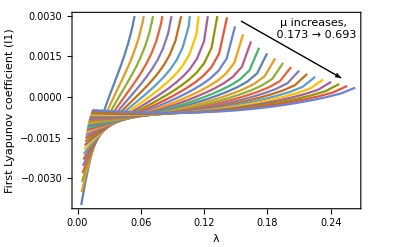

```mathematica
Show[ListLinePlot[l1μλ⟦;;,;;,2;;⟧,Frame->True,FrameLabel->{"λ","First Lyapunov coefficient (l1)"},FrameStyle->Black,Epilog->{Text["μ increases, \n 0.173 → 0.693",{.225,0.0025}]}],Graphics[Arrow[{{.155,.0028},{.25,.0007}}]]]
```

```mathematica
(*λ such that (κ^(**))'(λ)=0; vertical tangent line*)

μflat=Thread[{μ,((-9+14 μ)+√((-9+14 μ)^2+40μ(3+2μ)))/(10(3+2μ))}/.μ->Range[.173,.693,.02]];
```

```mathematica
(*Dim-2 bifurcation; λ at l1=0 for varying μ*)l1zeroλ=Table[{.153+.02ii,FindRoot[(l1/.LeqR/.Tb2fR/.κb2fR/.μ->(.153+.02ii) /.λ->λ1/.Thread[par->par1])==0,{λ1,μflat⟦ii,2⟧},AccuracyGoal->20]⟦1,2⟧},{ii,27}];
```

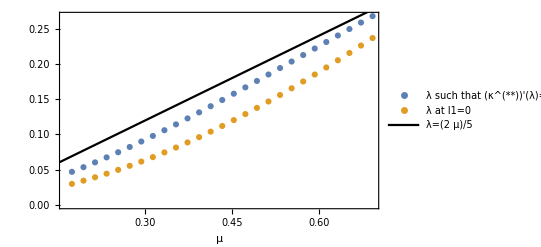

```mathematica
Show[ListPlot[{μflat,l1zeroλ},Frame->True,FrameLabel->{"μ",None},FrameStyle->Black,PlotLegends->Placed[{"λ such that (κ^(**))'(λ)=0","λ at l1=0"},{.78,.15}]],Plot[(2λ)/5,{λ,0,1},PlotStyle->Black,PlotLegends->Placed[{"λ=(2  μ)/5"},{.67,.33}]]]
```

```mathematica
(*This case*)l1zeroλ0=FindRoot[(l1/.LeqR/.Tb2fR/.κb2fR/.λ->λ1/.Thread[par->par1])==0,{λ1,.05},AccuracyGoal->20]⟦1,2⟧;
```

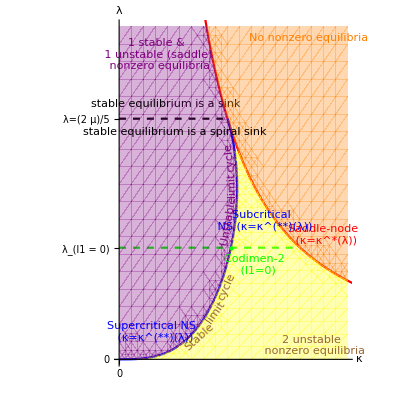

```mathematica
(*Bifurcation plane*)Show[(*Frame*)Plot[1,{x,0,.12},AspectRatio->1,PlotRange->{{0,1},{0,.12}},Ticks->{{0},{0,{(2μ)/5/.Thread[par->par1],"λ=(2  μ)/5"},{l1zeroλ0,"λ_(l1 = 0)"}}},AxesStyle->Black,AxesLabel->{κ,λ},Epilog->{Green,PointSize[Large],Point[{κ/.κb2fR/.λ->l1zeroλ0/.Thread[par->par1],l1zeroλ0}],Red,Text["Saddle-node \n (κ=κ^*(λ))",{.9,0.045}],Blue,Text["Supercritical NS \n (κ=κ^(**)(λ))",{.15,0.01}],Blue,Text["Subcritical \n NS (κ=κ^(**)(λ))",{.63,0.05}],Green,Text["Codimen-2 \n (l1=0)",{.6,0.034}],Orange,Text["No nonzero equilibria",{.83,0.116}],Brown,Text["2 unstable \n nonzero equilibria",{.85,0.005}],Purple,Text["1 stable & \n 1 unstable (saddle) \n nonzero equilibria",{.17,0.11}],Brown,Text[Rotate["Stable",42 Degree],{.35,0.008}],Brown,Text[Rotate["limit",55 Degree],{.42,0.017}],Brown,Text[Rotate["cycle",66 Degree],{.47,0.026}],Purple,Text[Rotate["Unstable",80 Degree],{.477,0.05}],Purple,Text[Rotate["limit",92 Degree],{.49,0.063}],Purple,Text[Rotate["cycle",97 Degree],{.485,0.073}],Black,Text["stable equilibrium is a sink",{.205,0.092}],Black,Text["stable equilibrium is a spiral sink",{.245,0.082}]}],ParametricPlot[{κ/.κbfR,λ1}/.λ->λ1/.Thread[par->par1],{λ1,0,μ/.Thread[par->par1]},PlotRange->{{0,1},{0,.12}},PlotStyle->Red],ParametricPlot[Evaluate[{κ/.κb2fR,λ1}/.λ->λ1/.Thread[par->par1]],{λ1,0,(2μ)/5/.Thread[par->par1]},PlotStyle->Blue](*,Plot[((-9+14 μ)+√((-9+14 μ)^2+40μ(3+2μ)))/(10(3+2μ))/.Thread[par->par1],{κ,0,κ/.κb2fR/.λ-> ((-9+14 μ)+√((-9+14 μ)^2+40μ(3+2μ)))/(10(3+2μ))/.Thread[par->par1]},PlotStyle->Dashed]*),Plot[l1zeroλ0,{x,0,κ/.κbfR/.λ->l1zeroλ0/.Thread[par->par1]},PlotStyle->{Green,Dashed}],Plot[(2μ)/5/.Thread[par->par1],{x,0,κ/.κbfR/.λ->(2μ)/5/.Thread[par->par1]},PlotStyle->{Black,Dashed}],RegionPlot[((κ/.κbfR/.λ->λ1/.Thread[par->par1])<κ1),{κ1,0,1},{λ1,0,.12},BoundaryStyle->None,PlotStyle->{Orange,Opacity[.3]}],RegionPlot[((κ/.κbfR)>κ1&&(κ/.κb2fR)<κ1)/.λ->λ1/.Thread[par->par1],{κ1,0,1},{λ1,0,(2μ)/5/.Thread[par->par1]},BoundaryStyle->None,PlotStyle->{Yellow,Opacity[.3]}],RegionPlot[(((κ/.κbfR)>κ1&&λ1>(2μ)/5)||(κ/.κb2fR)>κ1)/.λ->λ1/.Thread[par->par1],{κ1,0,1},{λ1,0,.12},BoundaryStyle->None,PlotStyle->{Purple,Opacity[.3]}]]
```

## Case studies

### κ-bifurcation diagrams

```mathematica
par1={0.135,0,.217,.5,0.045};

J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];
```

```mathematica
{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;
```

```mathematica
tkR=Ticks->{{{0,0},{κbp/.Thread[par->par1],SuperStar[κ]}},Thread[{{(μ λ)/(ω ρ),(5μ λ)/(2ω ρ)}/.Thread[par->par1],{(μ λ)/(ω ρ),(5μ λ)/(2ω ρ)}}]};
glR=GridLines->{{0,κbp},{2/5 T,T}/.TbfR/.Thread[par->par1]};
```

```mathematica
plt1=Show[ParametricPlot[{κR1,T},{T,Tκ0,Tbp},GridLinesStyle->Directive[{Black,Dashed}],Evaluate@{PlotStyle->Black,PlotRange->{{0,1},{0,1.3}},AxesLabel->{"κ","T"},glR,blRs},GridLinesStyle->Directive[Black,Dashing[{0,Small}],Thickness[20]],AspectRatio->1/GoldenRatio],ParametricPlot[{κR1,T},{T,Tbp,500},PlotStyle->{Dashed,Black}],Graphics[{EdgeForm[Thick],Black,Disk[{κbp,T/.TbfR}/.Thread[par->par1],{.015,.03}],White,Disk[{0,Tκ0}/.Thread[par->par1],{.015,.03}]}]];
```

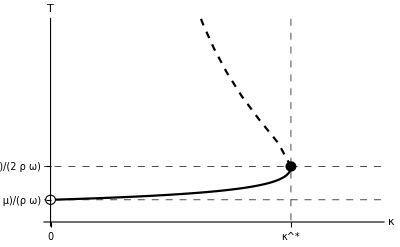

```mathematica
Show[plt1,tkR]
```

```mathematica
L1=NSolve[(((((ω L)/μ-1)/(κ L))^(3/2)/.κ->0.8κbp)==(L λ)/ρ)/.Thread[par->par1],L];
```

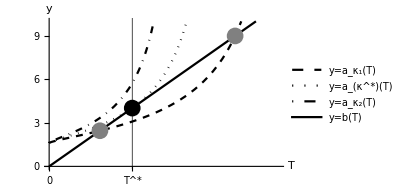

```mathematica
Plot[Evaluate[Append[(μ/(ω-μ κ T^(2/3)))/.κ->κbp{0.8,1,1.2},(T ρ)/λ]/.Thread[par->par1]],{T,0,1},PlotRange->{0,10},Ticks->{{0,{(L λ)/ρ/.L->Lbp/.Thread[par->par1],SuperStar[T]}},None},AxesLabel->{"T","y"},GridLines->{{(L λ)/ρ/.L->Lbp/.Thread[par->par1]},None},GridLinesStyle->Directive[{Black}],Epilog->{PointSize[0.04],Gray,Point[{(L λ)/ρ,L}/.Thread[par->par1]/.L1],PointSize[0.04],Black,Point[{(L λ)/ρ,L}/.L->Lbp/.Thread[par->par1]]},PlotStyle->{{Black,Dashed},{Black, Dotted},{Black,DotDashed},Black},LabelStyle->{{Black,Thick,12}},PlotLegends->Placed[{"y=a_κ_1(T)","y=a_(κ^*)(T)","y=a_κ_2(T)","y=b(T)"},{.82,.3}],ImageSize->300]
```

### Weak immune system

```mathematica
par1={0.05,0,μ1=.217,ρ1=.1,0.335};
```

```mathematica
J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];

{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;

TbpAllR=FindRoot[Simplify[#/.κeqR/.Thread[par->par1]]==0,{T,Mean@{Tκ0,Tbp}}]&/@{(*det1-1,*)tr1^2-4det1,det1-tr1+1};
κbpAll=κ/.κeqR/.TbpAllR/.Thread[par->par1];

TDbp=MapThread[{tr1,det1}/.{T->#1,κ->#2}&,{TbpAllR⟦;;,1,2⟧,κbpAll}];

κbpE=κbpAll⟦1⟧;
TbpE=T/.FindRoot[κR1==κbpE,{T,#}]&/@{Tκ0,2Tbp};
TDbpE=Thread[{tr1,det1}/.{T->TbpE,κ->κbpE}];

(*Case 1*)κ1=.5κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ1,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ1}];

(*Case 2*)κ2=Mean[κbpAll];
T2=T/.FindRoot[κR1==κ2,{T,#}]&/@{Tκ0,2Tbp};
TD2=Thread[{tr1,det1}/.{T->T2,κ->κ2}];
```

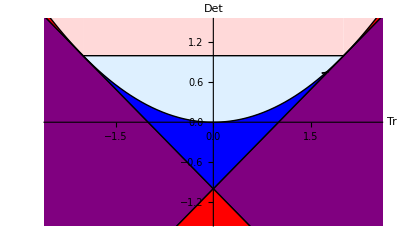

```mathematica
plotTD=Show[ParametricPlot[{tr1,det1}/.κeqR/.Thread[par->par1],{T,#⟦1⟧,#⟦2⟧},PlotStyle->#⟦3⟧]&/@{{Tκ0,2T1⟦2⟧,{Black,Dashed,Thick}},{Tκ0,Tbp,{Black,Thick}}}];

pr1={{1.65,1.82},{0.73,0.77}};Show[plotBF,plotTD,Graphics[{EdgeForm[Thick],Opacity[0],Rectangle@@({.95,1.05}Thread@pr1)}],PlotRange->{{-2.5,2.5},{-1.5,1.5}}]
```

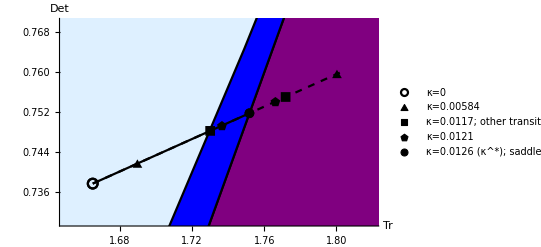

```mathematica
Show[plotBF,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE,TD2,{TDbp⟦2⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 10},{Graphics[RegularPolygon[5]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.00584","κ=0.0117; other transition (sink ↔ spiral sink)","κ=0.0121","κ=0.0126 (κ^*); saddle-node bifurcation (STABILITY change)"}],PlotRange->pr1]
```

```mathematica
stream=Table[Block[{k={κ1,κ2,2κ2}⟦ii⟧},Show[StreamPlot[SysF[{T,L},par/.κ->k/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,{300,70,70}⟦ii⟧},{L,0,{80,20,20}⟦ii⟧},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[k,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->k/.Thread[par->par1]/.T->Append[{T1,T2,{}}⟦ii⟧,0]],PlotMarkers->{★,◆,▲}⟦ii⟧,PlotStyle->Black]]],{ii,3}];

n=500;res=Table[Block[{parB=par/.κ->{κ1,κ2,2κ2}⟦jj⟧/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{jj,3},{ini,{{1,0},{10,10},{40,0},{100,0},{200,0}}}];

TLplot=ListLinePlot[#,PlotRange->All,Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotStyle->Thick,PlotLegends->(("{T_0,L_0}="<>ToString[#])&/@{{1,0},{10,10},{40,0},{100,0},{200,0}})]&/@res;
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;κ0=κ1;eps1=-10^-3;eps2=10^-3;n1=33;n2=34;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,500},{L,0,500},PlotStyle->{Black,Opacity[.2]},BoundaryStyle->{Black,Thick}];//Quiet
```

```mathematica
(*Stable manifold*)
(*κ2*)t1= T2⟦2⟧;κ0=κ2;eps1=-10^-3;eps2=10^-3;n1=30;n2=30;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin2=RegionPlot[mf[L]>T,{T,0,500},{L,0,500},PlotStyle->{Black,Opacity[.2]},BoundaryStyle->{Black,Thick}];//Quiet
```

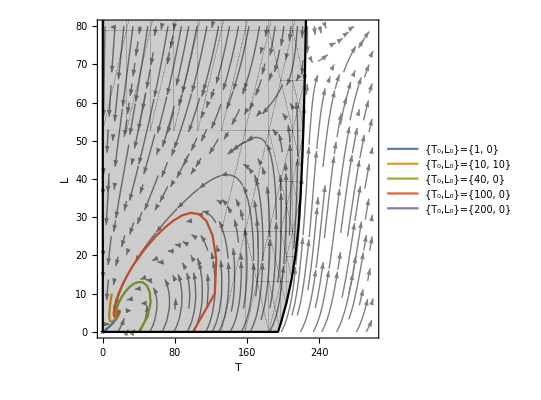
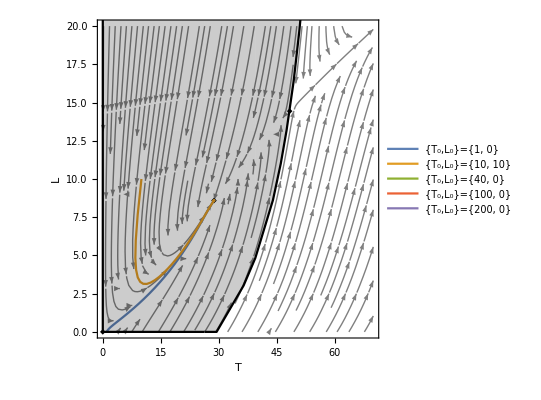
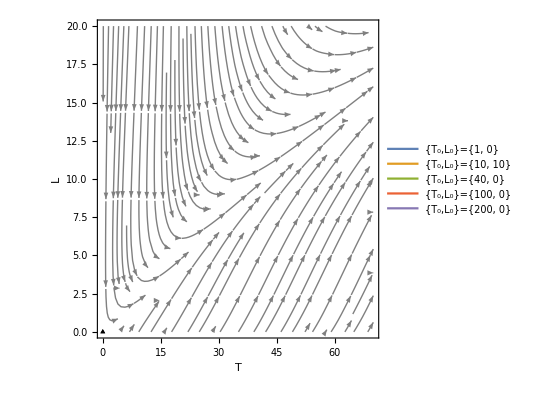

```mathematica
MapThread[Show,{stream,TLplot,{basin1,basin2,ListPlot[{500,500}]}}]
```

### Intermediate immune system

#### Basic

```mathematica
par1={.135,0,.217,.5,.045};
```

```mathematica
l1/.LeqR/.Tb2fR/.κb2fR/.Thread[par->par1]
```

0.000298475

```mathematica
J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];

{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;
```

```mathematica
TbpAllR=FindRoot[Simplify[#/.κp->κ/.κeqR/.Thread[par->par1]]==0,{T,Mean@{Tκ0,Tbp}}]&/@{det1-1,tr1^2-4det1,det1-tr1+1};
κbpAll=κ/.κeqR/.TbpAllR/.Thread[par->par1];
TDbp=MapThread[{tr1,det1}/.{T->#1,κ->#2}&,{TbpAllR⟦;;,1,2⟧,κbpAll}];
```

```mathematica
(*early BF*)κbpE1=κbpAll⟦1⟧;
TbpE1=T/.FindRoot[κR1==κbpE1,{T,#}]&/@{Tκ0,2Tbp};
TDbpE1=Thread[{tr1,det1}/.{T->TbpE1,κ->κbpE1}];

κbpE2=κbpAll⟦2⟧;
TbpE2=T/.FindRoot[κR1==κbpE2,{T,#}]&/@{Tκ0,2Tbp};
TDbpE2=Thread[{tr1,det1}/.{T->TbpE2,κ->κbpE2}];
```

```mathematica
(*Case 1*)κ1=.9κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ1,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ1}];
```

```mathematica
κ3=.98κbpAll⟦1⟧;
T3=T/.FindRoot[κR1==κ3,{T,#}]&/@{Tκ0,2Tbp};
TD3=Thread[{tr1,det1}/.{T->T3,κ->κ3}];
```

```mathematica
(*Case 2*)κ2=Mean[κbpAll⟦;;2⟧];
T2=T/.FindRoot[κR1==κ2,{T,#}]&/@{Tκ0,2Tbp};
TD2=Thread[{tr1,det1}/.{T->T2,κ->κ2}];
```

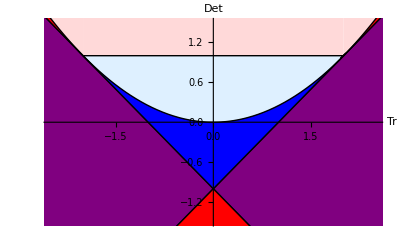

```mathematica
plotTD=Show[ParametricPlot[{tr1,det1}/.κeqR/.Thread[par->par1],{T,#⟦1⟧,#⟦2⟧},PlotStyle->#⟦3⟧]&/@{{Tκ0,2T1⟦2⟧,{Black,Dashed,Thick}},{Tκ0,Tbp,{Black,Thick}}}];

pr1={{1.944,2.1},{.95,1.09}};Show[plotBF,plotTD,Graphics[{EdgeForm[Thick],Opacity[0],Rectangle@@({.95,1.05}Thread@pr1)}],PlotRange->{{-2.5,2.5},{-1.5,1.5}}]
```

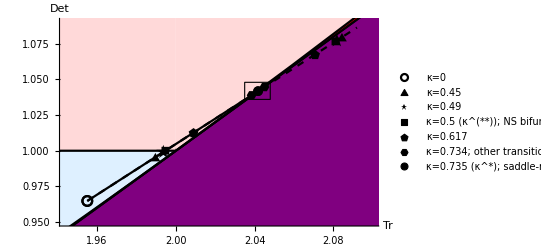

```mathematica
Show[Show[plotBF,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TD3,TDbpE1,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{"★",15},{Graphics[Rectangle[]], 8},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.45","κ=0.49","κ=0.5 (κ^(**)); NS bifurcation (STABILITY change)","κ=0.617","κ=0.734; other transition (source ↔ spiral source)","κ=0.735 (κ^*); saddle-node bifurcation"}],PlotRange->pr1],Graphics[{EdgeForm[Thick],Opacity[0],Rectangle@@(Thread@{{2.035,2.048},{1.036,1.048}})}]]
```

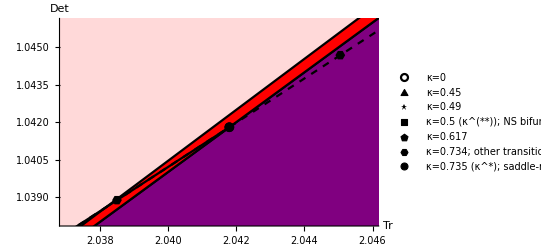

```mathematica
Show[plotBF,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,3TD1,TDbpE1,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{"★",15},{Graphics[Rectangle[]], 8},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.45","κ=0.49","κ=0.5 (κ^(**)); NS bifurcation (STABILITY change)","κ=0.617","κ=0.734; other transition (source ↔ spiral source)","κ=0.735 (κ^*); saddle-node bifurcation"}],PlotRange->{{2.037,2.046},{1.038,1.046}}]
```

#### No positive equilibrium (κ=2 κ_2)

```mathematica
stream=Table[Block[{k={κ1,κ2,2κ2}⟦ii⟧},Show[StreamPlot[SysF[{T,L},par/.κ->k/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,{2,1,1}⟦ii⟧},{L,0,{20,10,10}⟦ii⟧},
StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[k,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->k/.Thread[par->par1]/.T->Append[{T1,T2,{}}⟦ii⟧,0]],PlotMarkers->{★,◆,●}⟦ii⟧,PlotStyle->Black]]],{ii,3}];
```

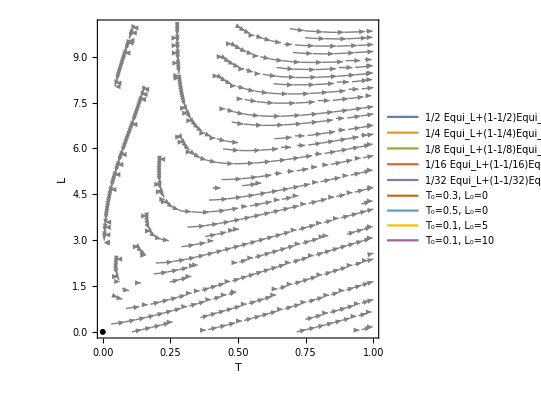

```mathematica
n=500;res=Table[Block[{parB=par/.κ->(2κ2)/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,{{.3,0},{.5,0},{10^-1,5},{10^-1,10}}}];Show[stream⟦3⟧,ListLinePlot[Join[{{0},{0},{0},{0},{0}},res],PlotRange->All,PlotStyle->Thick,PlotLegends->Join[(("1/"<>ToString[#]"Equi_L+(1-1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5},("T_0=0.1, L_0="<>ToString[#])&/@{5,10}]]]
```

#### No invariant closed curve (κ=κ_2)

```mathematica
(*Other case*)κ0=κ2;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,10},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->{Graphics[RegularPolygon[5]],5},PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=450;n2=318;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
(*resback1=Select[resback1,Positive[#⟦1⟧]&];*)
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
basin1=ListLinePlot[{resback1,resback2},PlotStyle->{{Black,Dashed,Thick}},PlotRange->{All,All}];
(*(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1⟧,resback2⟦;;⟧]];
basin1=RegionPlot[mf[T]<L,{T,0,2},{L,0,20},PlotStyle->{Opacity[0]},BoundaryStyle->{Black,Thick,Dashed},PlotRange->{{0,2},{0,10}}];//Quiet*)
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

```mathematica
n=700;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,Join[{T,L/.LeqR}/.T->(T1.{#,1-#})&/@(2^(-Range[5]))/.Thread[par->par1],{{.3,0},{.5,0}}]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,10}},Epilog->Point[res⟦;;,1⟧],PlotStyle->Thick,Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->Join[(("1/"<>ToString[#]"Equi_L+(1-1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5}]];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

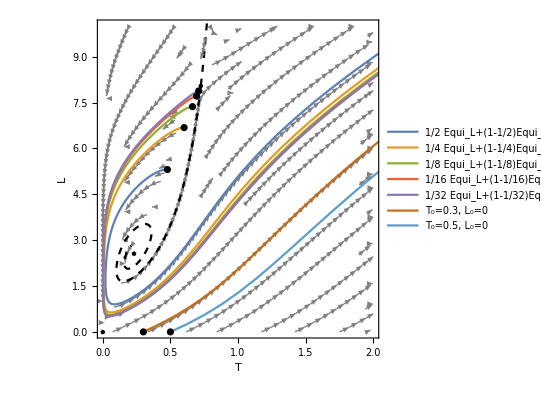

```mathematica
Show[stream,basin1,TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

#### Invariant closed curve (κ=.98κ^(**))

```mathematica
(*Other case*)κ0=.98κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,20},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->"★",PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=250;n2=249;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
basin1=ListLinePlot[{resback1,resback2},PlotRange->{All,All},PlotStyle->{{Black,Thick,Dashed}}];
(*manifold*)(*mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,20},PlotStyle->Opacity[0],BoundaryStyle->{Thick,Black,Dashed}];//Quiet*)
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

```mathematica
n=500;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,Join[{T,L/.LeqR}/.T->(T1.{#,1-#})&/@(2^(-Range[5]))/.Thread[par->par1],{{.3,0},{.5,0}}]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},PlotStyle->Thick,Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->(("(1/"<>ToString[#]")Equi_L+(1-1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5]))];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

```mathematica
(*limit cycle*)resbackLC=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini={T,L/.LeqR}/.T->(T1.{.4,.6})/.Thread[par->par1]},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,500]]⟦;;,;;2⟧;
```

```mathematica
ii=1; ang=0;
While[ang<2π,v1=resbackLC⟦-ii⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);v2=resbackLC⟦-ii-1⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);ang=ang+ArcCos[(v1.v2)/(Norm[v1]Norm[v2])];ii++;]
```

```mathematica
Show[stream,basin1,Graphics[{Opacity[.5],EdgeForm[Thick],Polygon@resbackLC⟦-ii;;⟧}],TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

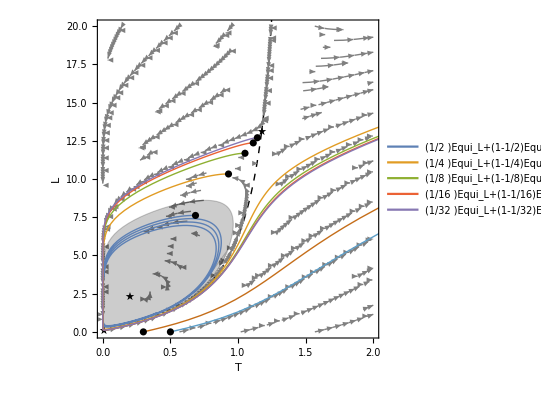

```mathematica
Area[Polygon@resbackLC⟦-ii;;⟧]
```

5.66183

#### No invariant closed curve (κ=.9κ^(**))

```mathematica
(*Other case*)κ0=.9κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,20},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->▲,PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=379;n2=305;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
(*resback1=Select[resback1,Positive[#⟦2⟧]&];*)
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,30},PlotStyle->{Black,Opacity[.2]},BoundaryStyle->None];//Quiet
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
basin2=ListLinePlot[{resback1,resback2},PlotStyle->{{Black,Thick,Dashed}}];
```

```mathematica
n=700;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,Join[{T,L/.LeqR}/.T->(T1.{#,1-#})&/@(2^(-Range[5]))/.Thread[par->par1],{{.3,0},{.5,0}}]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},PlotStyle->Thick,Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->Join[(("1/"<>ToString[#]"Equi_L+(1-1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5}]];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

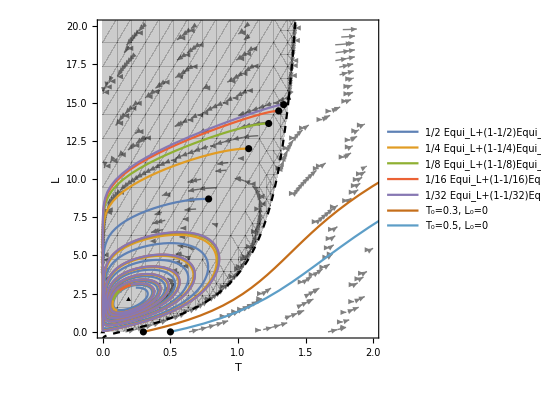

```mathematica
Show[stream,basin1,basin2,TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

#### Exclusive search invariant closed curve; With κ=(1-i/1000)κ^(**)

##### With κ=.999κ^(**)

```mathematica
(*Other case*)κ0=.999κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,20},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->●,PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=250;n2=149;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,20},BoundaryStyle->Dashed];//Quiet
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

```mathematica
resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
```

```mathematica
n=500;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,{T,L/.LeqR/.Thread[par->par1]}/.T->(T1.{1-#,#})&/@(2^(-Range[5]))}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->(("(1-1/"<>ToString[#]")Equi_L+(1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5]))];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

```mathematica
(*limit cycle*)resbackLC=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=(*{T,L/.LeqR}/.T->(T1.{1-.0625,.0625})/.Thread[par->par1]*){0.30394393142510984,2.5655708086550675}},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,100000]]⟦;;,;;2⟧;
ii=1; ang=0;
While[ang<2π,v1=resbackLC⟦-ii⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);v2=resbackLC⟦-ii-1⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);ang=ang+ArcCos[(v1.v2)/(Norm[v1]Norm[v2])];ii++;]
```

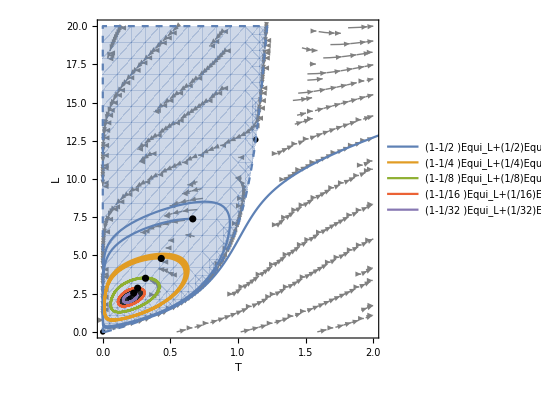

```mathematica
Show[stream,basin1,Graphics[{Opacity[.8],Polygon@resbackLC⟦-ii;;⟧}],TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

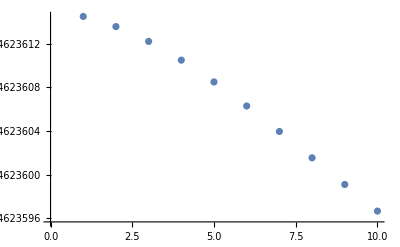

```mathematica
ListPlot[Area[Polygon@resbackLC⟦-(#+1)ii;;-# ii⟧]&/@Range[10]]
```

##### Search until LC disappears With κ=κ-κ^(**)/1000

```mathematica
er=1/10^6 Times@@({T,(T ρ)/λ}/.T->T1⟦2⟧/.Thread[par->par1])
```

0.0000142184

```mathematica
Clear@OneCycle;OneCycle[res0_,equil_]:=(jj=1;ang=0;While[ang<2π,v1=res0⟦-jj⟧-equil;v2=res0⟦-jj-1⟧-equil;ang=ang+ArcCos[(v1.v2)/(Norm[v1]Norm[v2])];jj++;];res0⟦-jj;;⟧);
```

```mathematica
(*equilibrium*){eq1,eq2}=Thread[{T,L/.LeqR/.Thread[par->par1]}/.T->T1];
κ1=.999κbpAll⟦1⟧;
resOneCycle={};
cycleH=resbackLC⟦-ii;;⟧;
```

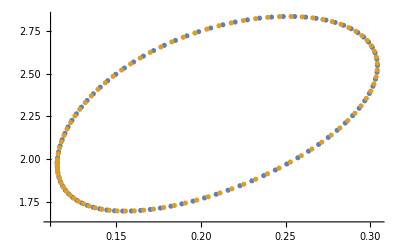

```mathematica
ListPlot[{cycleH,resbackLC⟦-2ii;;-ii⟧}]
```

```mathematica
(*κ1=(1-.001Length@resOneCycle)κbpAll⟦1⟧;
cycleH=resOneCycle⟦-1⟧;
resOneCycle=resOneCycle⟦;;-2⟧;*)
```

```mathematica
(For[kk=(*Length[resOneCycle]+*)2,kk<37,kk++,
(diff=1;
areaH=0;
resOneCycle=Append[resOneCycle,cycleH];
res=MinimalBy[resOneCycle⟦-1⟧,Norm];
κ1=κ1-.001κbpAll⟦1⟧;
parB=par/.κ->κ1/.Thread[par->par1];
While[diff>er/10,
(*running first map*)res={res⟦-1⟧};Do[res=Append[res,{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ1/.Thread[par->parB]]==res⟦-1⟧,Thread[{{T,L},res⟦-1⟧}]]];If[(!Positive[res⟦-1,1⟧])||(!Positive[res⟦-1,2⟧])||(Positive[res⟦-1,1⟧-10eq2⟦1⟧])||(Positive[res⟦-1,2⟧-100eq2⟦2⟧]),
(Print[kk];kk=100;diff=0;Break[])],{i,1000}];
If[kk≠100,(*find head, tail cycle*)(*cycleT=cycleH;*) cycleH=OneCycle[res,eq1];
(*find head, tail cycle*)areaT=areaH; areaH=Area[Polygon[cycleH]];
diff=Abs[areaH-areaT];]
];)
];resOneCycle=Append[resOneCycle,cycleH];)//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

36

{0.8687,Null}

```mathematica
(*resOneCycle>>"C:\\Users\\nyoon\\Documents\\Wolfram Mathematica\\resbackOneCycle";*)
(*resOneCycle=<<"C:\\Users\\nyoon\\Documents\\Wolfram Mathematica\\resbackOneCycle";*)
```

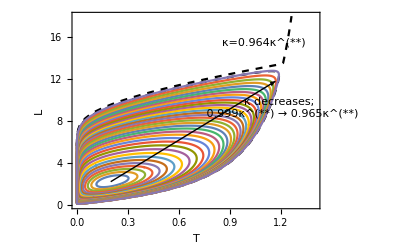

```mathematica
Show[ListLinePlot[res⟦;;⟧,PlotStyle->{{Black,Dashed}},PlotRange->{{0,1.4},{0,18}},Frame->True,FrameStyle->Black,FrameLabel->{T,L},Epilog->{Text["κ decreases; \n 0.999κ^(**) → 0.965κ^(**)",{1.2,9.3}],Text["κ=0.964κ^(**)",{1.1,15.5}]}],ListLinePlot[resOneCycle],Graphics[Arrow[{{T,L/.LeqR/.Thread[par->par1]}/.TbpAllR⟦1⟧,MaximalBy[cycleH,Norm]⟦1⟧+{.02,-1}}]]]
```

```mathematica
rg={{.45,.55},{0,1.3}};
```

```mathematica
smallplt=Show[ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,T/.TbpAllR⟦1⟧,1.4},PlotStyle->{{Black,Dotted,Thick}},AspectRatio->1,PlotRange->rg,Frame->True,FrameStyle->Red,FrameTicks->{None,None}],ListLinePlot[Table[{(1-ii/1000)κbpAll⟦1⟧,{Min,Max}⟦jj⟧@resOneCycle⟦ii,;;,1⟧},{jj,2},{ii,Length@resOneCycle,1,-1}],PlotStyle->{{Blue,Thick,Dotted}},Filling->{1->{2}}],ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,0,T/.TbpAllR⟦1⟧},PlotStyle->Black],Graphics[{EdgeForm[Thick],Black,Disk[{κbpAll⟦1⟧,TbpAllR⟦1,1,2⟧},{.0015,.018}]}]];
```

```mathematica
Show[ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,T/.TbpAllR⟦1⟧,3},PlotStyle->{{Black,Dotted,Thick}},AspectRatio->1,PlotRange->{{0,1},{0,1.5}},Frame->True,FrameStyle->Black,FrameLabel->{"κ","T^+"},Epilog->{EdgeForm[Thick],Inset[smallplt,{Right,Top},{Right,Top},Scaled[{.4,.4}]]}],ListLinePlot[Table[{(1-ii/1000)κbpAll⟦1⟧,{Min,Max}⟦jj⟧@resOneCycle⟦ii,;;,1⟧},{jj,2},{ii,Length@resOneCycle,1,-1}],PlotStyle->{{Blue,Thick,Dotted}},Filling->{1->{2}}],Graphics[{EdgeForm[Thick],Black,Disk[{κbpAll⟦1⟧,TbpAllR⟦1,1,2⟧},{.015,.02}],EdgeForm[Directive[Thin,Red]],Opacity[0],Rectangle@@(Thread@rg)}],Graphics[{Red,Arrow[{{.5,1.31},{.62,1.4}}]}],ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,0,T/.TbpAllR⟦1⟧},PlotStyle->Black]]
```

-Graphics-

### Strong immune system

#### Basic

```mathematica
par1={.135,0,.217,.5,.035};
```

```mathematica
l1/.LeqR/.Tb2fR/.κb2fR/.Thread[par->par1]
```

-0.000337604

```mathematica
FindRoot[(l1/.LeqR/.Tb2fR/.κb2fR/.λ->λ1/.Thread[par->par1])==0,{λ1,.05},AccuracyGoal->20]
```

{λ1→0.0402661}

```mathematica
J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];

{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;
```

```mathematica
TbpAllR=FindRoot[Simplify[#/.κp->κ/.κeqR/.Thread[par->par1]]==0,{T,Mean@{Tκ0,Tbp}}]&/@{det1-1,tr1^2-4det1,det1-tr1+1};
κbpAll=κ/.κeqR/.TbpAllR/.Thread[par->par1];
TDbp=MapThread[{tr1,det1}/.{T->#1,κ->#2}&,{TbpAllR⟦;;,1,2⟧,κbpAll}];
```

```mathematica
(*early BF*)κbpE1=κbpAll⟦1⟧;
TbpE1=T/.FindRoot[κR1==κbpE1,{T,#}]&/@{Tκ0,2Tbp};
TDbpE1=Thread[{tr1,det1}/.{T->TbpE1,κ->κbpE1}];

κbpE2=κbpAll⟦2⟧;
TbpE2=T/.FindRoot[κR1==κbpE2,{T,#}]&/@{Tκ0,2Tbp};
TDbpE2=Thread[{tr1,det1}/.{T->TbpE2,κ->κbpE2}];
```

```mathematica
(*Case 1*)κ1=.9κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ1,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ1}];
```

```mathematica
(*Case 2*)κ2=Mean[κbpAll⟦;;2⟧];
T2=T/.FindRoot[κR1==κ2,{T,#}]&/@{Tκ0,2Tbp};
TD2=Thread[{tr1,det1}/.{T->T2,κ->κ2}];
```

```mathematica
(*Case*)κ3=.94κbpAll⟦1⟧+.06κbpAll⟦3⟧;
T3=T/.FindRoot[κR1==κ3,{T,#}]&/@{Tκ0,2Tbp};
TD3=Thread[{tr1,det1}/.{T->T3,κ->κ3}];
```

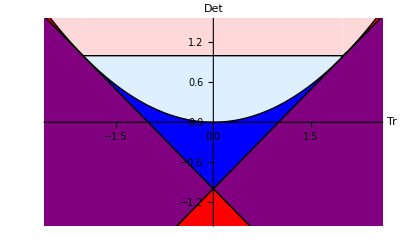

```mathematica
plotTD=Show[ParametricPlot[{tr1,det1}/.κeqR/.Thread[par->par1],{T,#⟦1⟧,#⟦2⟧},PlotStyle->#⟦3⟧]&/@{{Tκ0,2T1⟦2⟧,{Black,Dashed,Thick}},{Tκ0,Tbp,{Black,Thick}}}];

pr1={{1.9,2.15},{0.95,1.15}};Show[plotBF,plotTD,Graphics[{EdgeForm[Thick],Opacity[0],Rectangle@@(Transpose@pr1)}],PlotRange->{2.5{-1,1},1.5{-1,1}}]
```

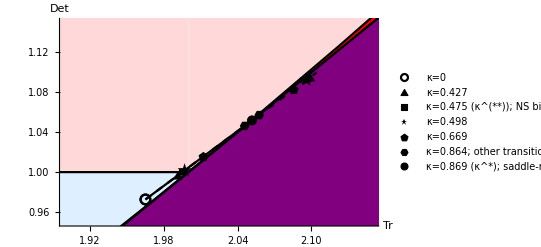

```mathematica
Show[plotBF,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE1,TD3,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 7},{"★",15},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ="<>ToString[Round[κ1,.001]],"κ="<>ToString[Round[κbpAll⟦1⟧,.001]]<>" (κ^(**)); NS bifurcation (STABILITY change)","κ="<>ToString[Round[κ3,.001]],"κ="<>ToString[Round[κ2,.001]],"κ="<>ToString[Round[κbpAll⟦2⟧,.001]]<>"; other transition (source ↔ spiral source)","κ="<>ToString[Round[κbpAll⟦3⟧,.001]]<>" (κ^*); saddle-node bifurcation"}],PlotRange->pr1]
```

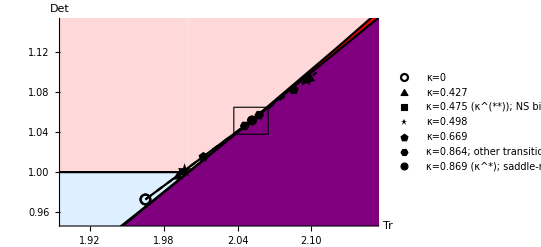

```mathematica
Show[Show[plotBF3,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE1,TD3,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 7},{"★",15},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ="<>ToString[Round[κ1,.001]],"κ="<>ToString[Round[κbpAll⟦1⟧,.001]]<>" (κ^(**)); NS bifurcation (STABILITY change)","κ="<>ToString[Round[κ3,.001]],"κ="<>ToString[Round[κ2,.001]],"κ="<>ToString[Round[κbpAll⟦2⟧,.001]]<>"; other transition (source ↔ spiral source)","κ="<>ToString[Round[κbpAll⟦3⟧,.001]]<>" (κ^*); saddle-node bifurcation"}],PlotRange->pr1],Graphics[{EdgeForm[Thick],Opacity[0],Rectangle@@({.002,.017}+Thread@{{2.035,2.048},{1.036,1.048}})}]]
```

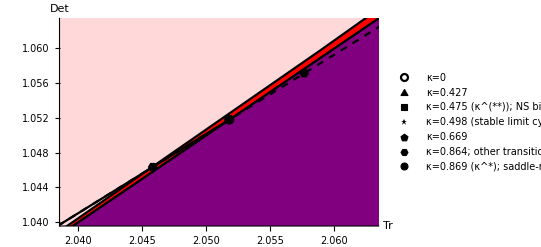

```mathematica
Show[plotBF3,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE1,TD3,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 7},{"★",15},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ="<>ToString[Round[κ1,.001]],"κ="<>ToString[Round[κbpAll⟦1⟧,.001]]<>" (κ^(**)); NS bifurcation (STABILITY change)","κ="<>ToString[Round[κ3,.001]]<>" (stable limit cycle)","κ="<>ToString[Round[κ2,.001]],"κ="<>ToString[Round[κbpAll⟦2⟧,.001]]<>"; other transition (source ↔ spiral source)","κ="<>ToString[Round[κbpAll⟦3⟧,.001]]<>" (κ^*); saddle-node bifurcation"}],PlotRange->{{.002,.017}+{2.037,2.046},{.002,.017}+{1.038,1.046}}]
```

#### No positive equilibrium (κ=2 κ_2)

```mathematica
stream=Table[Block[{k={κ1,κ2,2κ2}⟦ii⟧},Show[StreamPlot[SysF[{T,L},par/.κ->k/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,{2,1,2}⟦ii⟧},{L,0,{25,10,10}⟦ii⟧},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[k,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->k/.Thread[par->par1]/.T->Append[{T1,T2,{}}⟦ii⟧,0]],PlotMarkers->{★,◆,●}⟦ii⟧,PlotStyle->Black]]],{ii,3}];
```

```mathematica
n=500;res=Table[Block[{parB=par/.κ->{κ1,κ2,2κ2}⟦jj⟧/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{jj,3},{ini,{{1.3,10},{.2,2},{.7,7}}}];
TLplot=ListLinePlot[#,PlotRange->All,PlotStyle->Black(*,Epilog->{PointSize[Medium],Point[{#⟦1,;;2⟧}]}*),Frame->True,FrameLabel->{"T","L"},FrameStyle->Black]&/@res;(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;κ0=κ1;eps1=-10^-3;eps2=10^-3;n1=379;n2=300;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,25}];//Quiet
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

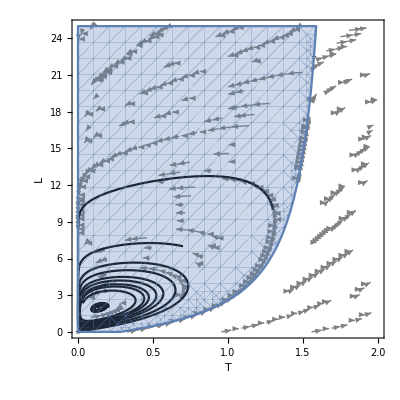
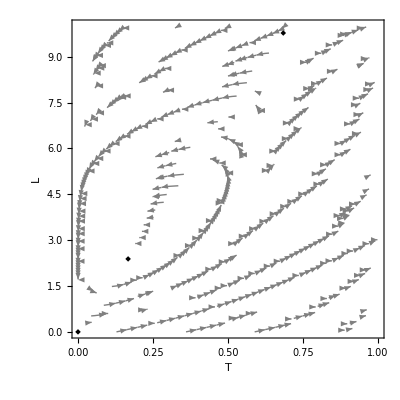
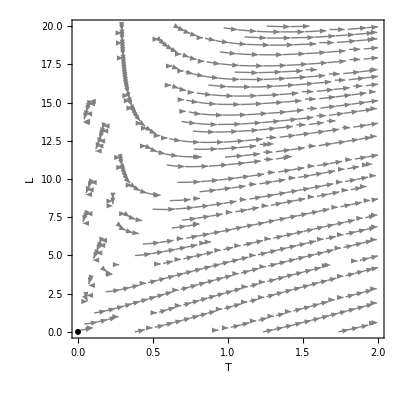

```mathematica
MapThread[Show,{stream,TLplot,{basin1,ListPlot[{500,500}],ListPlot[{500,500}]}}]
```

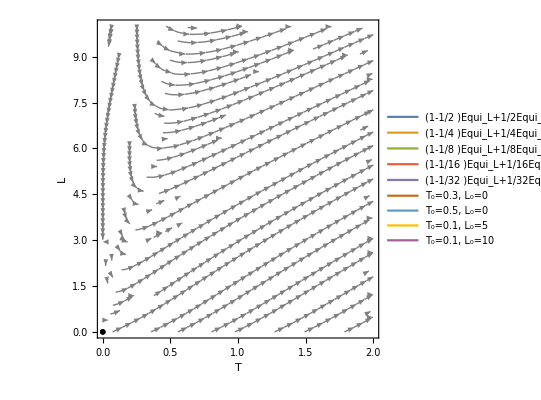

```mathematica
res=Table[Block[{parB=par/.κ->(2κ2)/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,{{.3,0},{.5,0},{10^-1,5},{10^-1,10}}}];Show[stream⟦3⟧,ListLinePlot[Join[{{0},{0},{0},{0},{0}},res],PlotStyle->Thick,PlotLegends->Join[(("(1-1/"<>ToString[#]")Equi_L+1/"<>ToString[#]<>"Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5},("T_0=0.1, L_0="<>ToString[#])&/@{5,10}]]]
```

#### No invariant closed curve (κ=κ_2)

```mathematica
(*Other case*)κ0=κ2;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,10},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->{Graphics[RegularPolygon[5]],5},PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=401;n2=153;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
basin1=ListLinePlot[{resback1,resback2},PlotStyle->{{Black,Thick,Dashed}},PlotRange->All];
(*(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1⟧,resback2⟦;;⟧]];
basin1=RegionPlot[mf[T]<L,{T,0,2},{L,0,20},BoundaryStyle->{Dashed,Black,Thick},PlotStyle->Opacity[0]];//Quiet*)
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

```mathematica
n=700;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,Join[{T,L/.LeqR}/.T->(T1.{1-#,#})&/@(2^(-Range[5]))/.Thread[par->par1],{{.3,0},{.5,0}}]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},PlotStyle->Thick,Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->Join[(("(1-1/"<>ToString[#]")Equi_L+(1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5}]];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

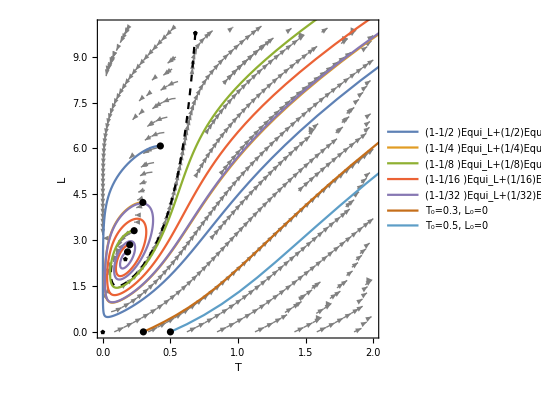

```mathematica
Show[stream,basin1,TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

#### Invariant closed curve around κ^(**) (κ=.94κ^(**)+.06κ^*)

```mathematica
(*J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];

{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;*)
```

```mathematica
(*TbpAllR=FindRoot[Simplify[#/.κp->κ/.κeqR/.Thread[par->par1]]==0,{T,Mean@{Tκ0,Tbp}}]&/@{det1-1,tr1^2-4det1,det1-tr1+1};
κbpAll=κ/.κeqR/.TbpAllR/.Thread[par->par1];
TDbp=MapThread[{tr1,det1}/.{T->#1,κ->#2}&,{TbpAllR⟦;;,1,2⟧,κbpAll}];
```

```mathematica
(*(*early BF*)κbpE1=κbpAll⟦1⟧;
TbpE1=T/.FindRoot[κR1==κbpE1,{T,#}]&/@{Tκ0,2Tbp};
TDbpE1=Thread[{tr1,det1}/.{T->TbpE1,κ->κbpE1}];

κbpE2=κbpAll⟦2⟧;
TbpE2=T/.FindRoot[κR1==κbpE2,{T,#}]&/@{Tκ0,2Tbp};
TDbpE2=Thread[{tr1,det1}/.{T->TbpE2,κ->κbpE2}];
```

```mathematica
κbpAll
```

{0.474514,0.864389,0.869459}

```mathematica
.935κbpAll⟦1⟧+.065κbpAll⟦3⟧
```

0.500186

```mathematica
(*Other case*)κ0=.94κbpAll⟦1⟧+.06κbpAll⟦3⟧;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,20},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->"★",PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=350;n2=260;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
basin1=ListLinePlot[{resback1,resback2},PlotRange->{All,All},PlotStyle->{{Black,Dashed,Thick}},Filling->20];
(*(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,20},BoundaryStyle->Dashed];//Quiet*)
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

```mathematica
n=700;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,Join[{T,L/.LeqR}/.T->(T1.{1-#,#})&/@(2^(-Range[5]))/.Thread[par->par1],{{.3,0},{.5,0}}]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},PlotStyle->Thick,Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->Join[(("(1-1/"<>ToString[#]")Equi_L+(1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5}]];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

```mathematica
(*limit cycle*)resLC=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini={T,L/.LeqR}/.T->(T1.{.7,.3})/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,5000]]⟦;;,;;2⟧;
ii=1; ang=0;
While[ang<2π,v1=resLC⟦-ii⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);v2=resLC⟦-ii-1⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);ang=ang+ArcCos[(v1.v2)/(Norm[v1]Norm[v2])];ii++;]
```

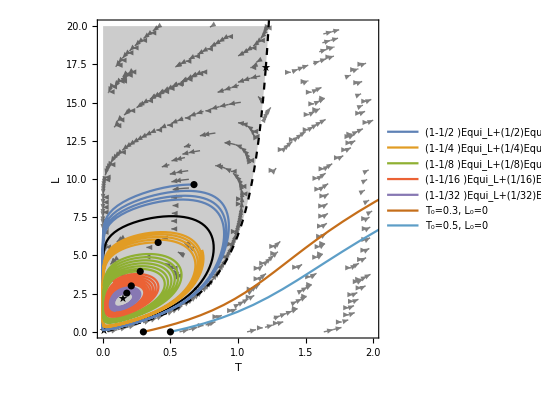

```mathematica
Show[stream,basin1,ListLinePlot[resLC⟦-ii;;⟧,PlotStyle->{{Black,Thick}}],TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

#### No invariant closed curve (κ=κ_1)

```mathematica
(*Other case*)κ0=κ1;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,30},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->κ0/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->▲,PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=380;n2=300;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,30},PlotStyle->{Black,Opacity[.2]},BoundaryStyle->None];//Quiet
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
basin2=ListLinePlot[{resback1,resback2},PlotRange->All,PlotStyle->{{Black,Dashed,Thick}}];
```

```mathematica
n=700;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,Join[{T,L/.LeqR}/.T->(T1.{1-#,#})&/@(2^(-Range[5]))/.Thread[par->par1],{{.3,0},{.5,0}}]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},PlotStyle->Thick,Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->Join[(("(1-1/"<>ToString[#]")Equi_L+(1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5])),("T_0="<>ToString[#]<>", L_0=0")&/@{.3,.5}]];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

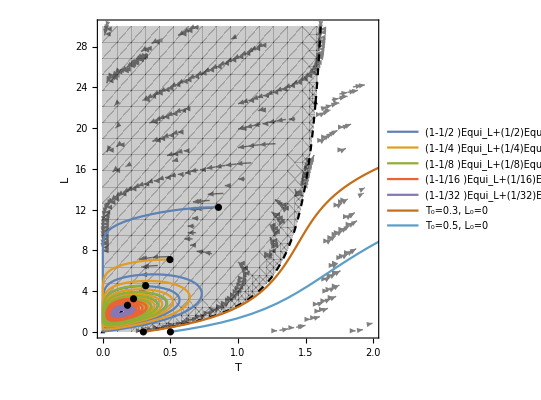

```mathematica
Show[stream,basin1,basin2,TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

#### Exclusive search invariant closed curve; With κ=(1-i/1000)κ^*+i/1000 κ^(**))

##### With κ=.999κ^(**)+.001κ^*

```mathematica
(*Other case*)κ0=.999κbpAll⟦1⟧+.001κbpAll⟦3⟧;
T1=T/.FindRoot[κR1==κ0,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ0}];
```

```mathematica
stream=Show[StreamPlot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,2},{L,0,20},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[κ0,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.Thread[par->par1]/.T->Append[T1,0]],PlotMarkers->●,PlotStyle->Black]];
```

```mathematica
(*Stable manifold*)
(*κ1*)t1= T1⟦2⟧;eps1=-10^-3;eps2=10^-3;n1=350;n2=149;

(*Eivenvector of eigenvalue<1*)v=SortBy[Thread@Eigensystem[J1/.T->t1/.κ->κ0],Abs[#⟦1⟧]&]⟦1,2⟧;
(*first part of manifold*)resback1=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps1 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n1]]⟦;;,;;2⟧;
resback1=Select[resback1,Positive[#⟦2⟧]&];
(*second part of manifold*)resback2=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini=({T,L}/.LeqR/.T->t1/.Thread[par->par1])+eps2 v},NestList[{T,L}/.FindRoot[SysF[{T,L},par/.κ->κ0/.Thread[par->par1]]==#,Thread[{{T,L},{T,L}/.LeqR/.T->t1/.Thread[par->par1]}]]&,ini,n2]]⟦;;,;;2⟧;
(*manifold*)mf=Interpolation[Join[resback1⟦-1;;1;;-1,2;;1;;-1⟧,resback2⟦;;,2;;1;;-1⟧]];
basin1=RegionPlot[mf[L]>T,{T,0,2},{L,0,20},BoundaryStyle->Dashed];//Quiet
(*Graphics[{EdgeForm[None],FaceForm[Opacity[.5],Gray],
Polygon[Join[resback1⟦-1;;1;;-1⟧,resback2,{{0,resback2⟦-1,2⟧},{0,0}}]]},Axes->True];*)
```

```mathematica
n=700;res=Table[Block[{parB=par/.κ->κ0/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{ini,{T,L/.LeqR}/.T->(T1.{1-#,#})&/@(2^(-Range[5]))/.Thread[par->par1]}];
TLplot=ListLinePlot[res,PlotRange->{{0,2},{0,20}},Epilog->Point[res⟦;;,1⟧],Frame->True,FrameLabel->{"T","L"},FrameStyle->Black,PlotLegends->(("(1-1/"<>ToString[#]")Equi_L+(1/"<>ToString[#]<>")Equi_H")&/@(2^Range[5]))];(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

```mathematica
(*limit cycle*)resLC=Block[{parB=par/.κ->κ0/.Thread[par->par1],ini={T,L/.LeqR}/.T->(T1.{.9,.1})/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,800000]]⟦;;,;;2⟧;

ii=1; ang=0;
While[ang<2π,v1=resLC⟦-ii⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);v2=resLC⟦-ii-1⟧-({T,L/.LeqR/.Thread[par->par1]}/.T->T1⟦1⟧);ang=ang+ArcCos[(v1.v2)/(Norm[v1]Norm[v2])];ii++;]
```

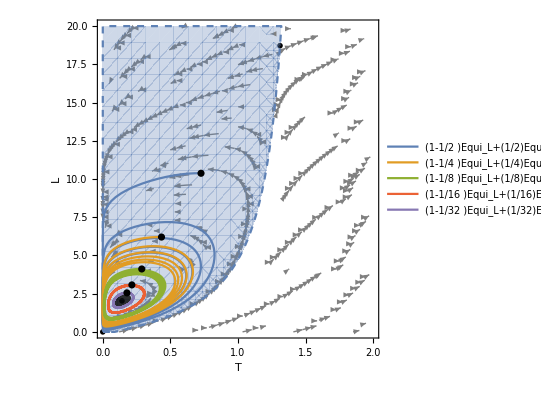

```mathematica
Show[stream,basin1,Graphics[{Opacity[.8],Polygon@resLC⟦-ii;;⟧}],TLplot,ListPlot[res⟦;;,1⟧,PlotStyle->Black]]
```

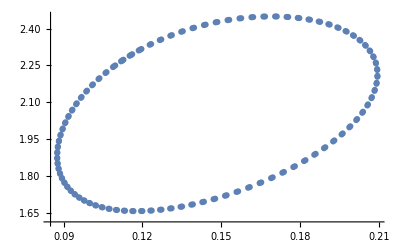

```mathematica
Show[ListPlot[resLC⟦-2ii;;-ii⟧],ListPlot[resLC⟦-ii;;⟧]]
```

##### Search until LC disappears With κ=κ+(κ^(**)-κ^(**))/1000

```mathematica
er=1/10^6 Times@@({T,(T ρ)/λ}/.T->T1⟦2⟧/.Thread[par->par1])
```

0.0000245315

```mathematica
Clear@OneCycle;OneCycle[res0_,equil_]:=(jj=1;ang=0;While[ang<2π,v1=res0⟦-jj⟧-equil;v2=res0⟦-jj-1⟧-equil;ang=ang+ArcCos[(v1.v2)/(Norm[v1]Norm[v2])];jj++;];res0⟦-jj;;⟧);
```

```mathematica
(*equilibrium*){eq1,eq2}=Thread[{T,L/.LeqR/.Thread[par->par1]}/.T->T1];
κ1=.999κbpAll⟦1⟧+.001κbpAll⟦3⟧;
resOneCycle={};
cycleH=resLC⟦-ii;;⟧;
```

```mathematica
For[kk=2,kk<70,kk++,
(diff=1;
areaH=0;
resOneCycle=Append[resOneCycle,cycleH];
res=MaximalBy[resOneCycle⟦-1⟧,Norm];
κ1=κ1+.001(κbpAll⟦3⟧-κbpAll⟦1⟧);
parB=par/.κ->κ1/.Thread[par->par1];
While[diff>er/10,
(*running first map*)res={res⟦-1⟧};Do[res=Append[res,SysF[res⟦-1⟧,parB]];If[(*(Im[res⟦-1⟧]≠{0,0})||*)(res⟦-1,1⟧>10eq2⟦1⟧),
(Print[kk];kk=100;diff=0;Break[])],{i,1000}];
If[kk≠100,(*find head, tail cycle*)(*cycleT=cycleH;*) cycleH=OneCycle[res,eq1];
(*find head, tail cycle*)areaT=areaH; areaH=Area[Polygon[cycleH]];
diff=Abs[areaH-areaT];]
];)
];resOneCycle=Append[resOneCycle,cycleH];
```

65

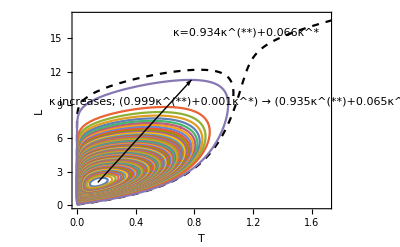

```mathematica
Show[ListLinePlot[res⟦-310;;⟧,PlotStyle->{{Black,Dashed}},PlotRange->{{0,1.7},{0,17}},Frame->True,FrameStyle->Black,FrameLabel->{T,L},Epilog->{Text["κ increases; (0.999κ^(**)+0.001κ^*) → (0.935κ^(**)+0.065κ^*)",{1.05,9.3}],Text["κ=0.934κ^(**)+0.066κ^*",{1.15,15.5}]}],ListLinePlot[resOneCycle],Graphics[Arrow[{{T,L/.LeqR/.Thread[par->par1]}/.TbpAllR⟦1⟧,MaximalBy[cycleH,Norm]⟦1⟧}]]]
```

```mathematica
(*resOneCycle>>"C:\\Users\\nyoon\\Documents\\Wolfram Mathematica\\resOneCycle";*)
(*resOneCycle=<<"C:\\Users\\nyoon\\Documents\\Wolfram Mathematica\\resOneCycle";*)
```

```mathematica
rg={{.45,.53},{0,1.3}};
```

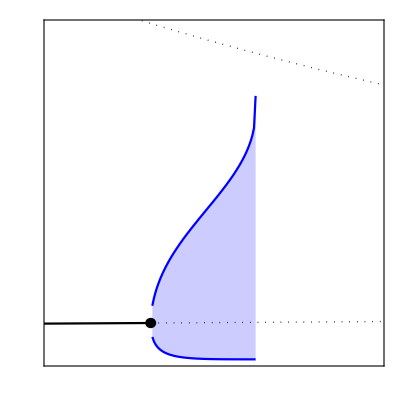

```mathematica
smallplt=Show[ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,T/.TbpAllR⟦1⟧,3},PlotStyle->{{Black,Dotted,Thick}},AspectRatio->1,PlotRange->rg,Frame->True,FrameStyle->Red,FrameTicks->{None,None}],ListLinePlot[Table[{κbpAll⟦1⟧+(κbpAll⟦3⟧-κbpAll⟦1⟧)/1000 ii,{Min,Max}⟦jj⟧@resOneCycle⟦ii,;;,1⟧},{jj,2},{ii,Length@resOneCycle}],PlotStyle->Blue,Filling->{1->{2}}],Graphics[{EdgeForm[Thick],Black,Disk[{κbpAll⟦1⟧,TbpAllR⟦1,1,2⟧},{.0012,.018}]}],ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,0,T/.TbpAllR⟦1⟧},PlotStyle->Black]]
```

```mathematica
Show[ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,T/.TbpAllR⟦1⟧,3},PlotStyle->{{Black,Dotted,Thick}},AspectRatio->1,PlotRange->{{0,1},{0,1.5}},Frame->True,FrameStyle->Black,FrameLabel->{"κ","T^+"},Epilog->{EdgeForm[Thick],Inset[smallplt,{Right,Top},{Right,Top},Scaled[{.4,.4}]]}],ListLinePlot[Table[{κbpAll⟦1⟧+(κbpAll⟦3⟧-κbpAll⟦1⟧)/1000 ii,{Min,Max}⟦jj⟧@resOneCycle⟦ii,;;,1⟧},{jj,2},{ii,Length@resOneCycle}],PlotStyle->Blue,Filling->{1->{2}}],Graphics[{EdgeForm[Thick],Black,Disk[{κbpAll⟦1⟧,TbpAllR⟦1,1,2⟧},{.015,.02}],EdgeForm[Directive[Thin,Red]],Opacity[0],Rectangle@@(Thread@rg)}],Graphics[{Red,Arrow[{{.5,1.31},{.62,1.4}}]}],ParametricPlot[{κ/.κeqR/.Thread[par->par1],T},{T,0,T/.TbpAllR⟦1⟧},PlotStyle->Black]]
```

-Graphics-